```mathematica
g=Graph[EdgeList[EdgeAdd[WheelGraph[6,VertexLabels->"Name"],{2 <->7,3 <->7,3 <->8,4 <->8,7 <->8}]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"];
```

```mathematica
FindFullFormula4[g]
```

{v1x28x35x467,v1x258x3x467,v1x258x36x47,v18x2x35x467,v18x25x3x467,v18x25x36x47,v18x24x36x57,v18x24x35x67,v17x28x35x46,v17x258x3x46,v17x258x36x4,v17x24x36x58,v17x24x35x68}

```mathematica
ColorGraph[g_,set_]:=Block[{color={Red,Green,Blue,Yellow}},
Graph[g,VertexStyle->Flatten[Table[Table[vertex->color[[i]],{vertex,set[[i]]}],{i,Length[set]}]],
VertexSize->Large]
]
```

```mathematica
FilterSymbol[sym_,vertices_]:=Block[{v2=SymbolToSets[sym]},
v2=Map[Select[#,MemberQ[vertices,#]&]&,v2];
v2=Select[v2,#≠{}&];
v2=Sort[Map[Sort[#]&,v2],#1[[1]]<#2[[1]]&];
Simplify[SetsToSymbol[v2]]
]
```

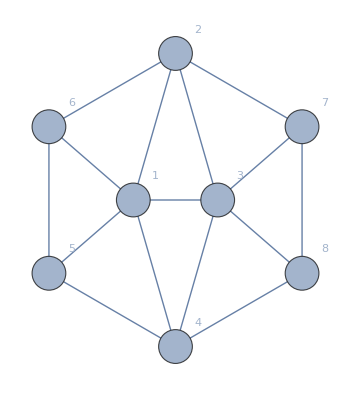
{-Graphics-{v2x35x46,v1x28x47},-Graphics-{v25x3x46,v1x28x47},-Graphics-{v25x36x4,v1x28x47},-Graphics-{v2x35x46,v18x2x47},-Graphics-{v25x3x46,v18x2x47},-Graphics-{v25x36x4,v18x2x47},-Graphics-{v24x36x5,v18x24x7},-Graphics-{v24x35x6,v18x24x7},-Graphics-{v2x35x46,v17x28x4},-Graphics-{v25x3x46,v17x28x4},-Graphics-{v25x36x4,v17x28x4},-Graphics-{v24x36x5,v17x24x8},-Graphics-{v24x35x6,v17x24x8}}

```mathematica
Map[Labeled[Graph[ColorGraph[g,SymbolToSets [#]],GraphHighlight->EdgeList[WheelGraph[6]]],
{FilterSymbol[#,{2,3,4,5,6}],FilterSymbol[#,{1,4,8,7,2}]}]&,FindFullFormula4[g]]
```

```mathematica
h=EdgeAdd[EdgeDelete[g,{1<->3}],2<->4];
```

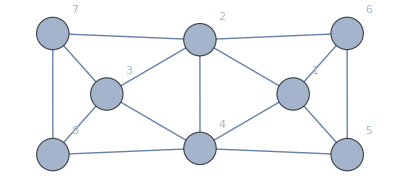
{-Graphics-{25♁46,28},-Graphics-{25,28♁47},-Graphics-{25,28},-Graphics-{25♁46,47},-Graphics-{25,47},-Graphics-{46,28♁47},-Graphics-{46,28},-Graphics-{46,47},-Graphics-{25♁36,17♁28},-Graphics-{25♁46,17♁28},-Graphics-{35♁46,17♁28},-Graphics-{25♁36,18♁47},-Graphics-{25♁46,18♁47},-Graphics-{35♁46,18♁47},-Graphics-{25♁36,28♁47},-Graphics-{25♁46,28♁47},-Graphics-{35♁46,28♁47}}

```mathematica
Map[Labeled[Graph[ColorGraph[EdgeList[h],SymbolToSets [#]],VertexLabels->"Name"],
{SymbolToLabel2[FilterSymbol[#,{2,3,4,5,6}]],SymbolToLabel2[FilterSymbol[#,{1,4,8,7,2}]]}]&,Sort[FindFullFormula4[h],CompareSymbols]]
```

```mathematica
h2=EdgeAdd[EdgeDelete[g,{1<->6}],2<->5];
```

```mathematica
Map[Labeled[Graph[ColorGraph[EdgeList[h2],SymbolToSets [#]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->130],
{SymbolToLabel2[FilterSymbol[#,{2,3,4,5,6}]],SymbolToLabel2[FilterSymbol[#,{1,4,8,7,2}]]}]&,Sort[FindFullFormula4[h2],CompareSymbols]]
```

{-Graphics-{24♁35,17♁24},-Graphics-{24,17♁24},-Graphics-{35,17♁28},-Graphics-{24♁35,18♁24},-Graphics-{24,18♁24},-Graphics-{35,18♁47},-Graphics-{35,28♁47},-Graphics-{24♁35,17♁24},-Graphics-{24♁36,17♁24},-Graphics-{35♁46,17♁28},-Graphics-{24♁35,18♁24},-Graphics-{24♁36,18♁24},-Graphics-{35♁46,18♁47},-Graphics-{35♁46,28♁47}}

```mathematica
h3=EdgeDelete[g,{1<->6}];
```

```mathematica
Map[Labeled[Graph[ColorGraph[EdgeList[h3],SymbolToSets [#]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->130],
{SymbolToLabel2[FilterSymbol[#,{2,3,4,5,6}]],SymbolToLabel2[FilterSymbol[#,{1,4,8,7,2}]]}]&,Sort[FindFullFormula4[h3],CompareSymbols]]
```

{-Graphics-{24♁35,17♁24},-Graphics-{24,17♁24},-Graphics-{25,17♁28},-Graphics-{35,17♁28},-Graphics-{24♁35,18♁24},-Graphics-{24,18♁24},-Graphics-{25,18♁47},-Graphics-{35,18♁47},-Graphics-{25,28♁47},-Graphics-{35,28♁47},-Graphics-{24♁35,17♁24},-Graphics-{24♁36,17♁24},-Graphics-{25♁36,17♁28},-Graphics-{25♁46,17♁28},-Graphics-{35♁46,17♁28},-Graphics-{24♁35,18♁24},-Graphics-{24♁36,18♁24},-Graphics-{25♁36,18♁47},-Graphics-{25♁46,18♁47},-Graphics-{35♁46,18♁47},-Graphics-{25♁36,28♁47},-Graphics-{25♁46,28♁47},-Graphics-{35♁46,28♁47}}

```mathematica
h4=EdgeDelete[g,{1<->4}];
```

```mathematica
Map[Labeled[Graph[ColorGraph[EdgeList[h4],SymbolToSets [#]],VertexLabels->"Name",GraphLayout->"TutteEmbedding",ImageSize->130],
{SymbolToLabel2[FilterSymbol[#,{2,3,4,5,6}]],SymbolToLabel2[FilterSymbol[#,{1,4,8,7,2}]]}]&,Sort[FindFullFormula4[h4],CompareSymbols]]
```

{-Graphics-{25,147♁28},-Graphics-{25♁36,147},-Graphics-{25,147},-Graphics-{35,147♁28},-Graphics-{36,147♁28},-Graphics-{35,147},-Graphics-{36,147},-Graphics-{25♁36,14♁28},-Graphics-{25,14♁28},-Graphics-{35,14♁28},-Graphics-{36,14♁28},-Graphics-{24♁35,17♁24},-Graphics-{24♁36,17♁24},-Graphics-{25♁36,17♁28},-Graphics-{25♁46,17♁28},-Graphics-{35♁46,17♁28},-Graphics-{24♁35,18♁24},-Graphics-{24♁36,18♁24},-Graphics-{25♁36,18♁47},-Graphics-{25♁46,18♁47},-Graphics-{35♁46,18♁47},-Graphics-{25♁36,28♁47},-Graphics-{25♁46,28♁47},-Graphics-{35♁46,28♁47}}